```mathematica
ElmoBumpyCartWedge[X_,Y_,μ_,I_,NumCoils_,Rcoils_,a_,γ_,Iwdg_]:=μ/(2 π) Sum[

I/((X-(Rcoils-a)Cos[2 π i/NumCoils])^2+(Y-(Rcoils-a)Sin[2 π i/NumCoils])^2){(Rcoils-a)Sin[2 π i/NumCoils]-Y,X-(Rcoils-a)Cos[2 π i/NumCoils]}

-I/((X-(Rcoils+a)Cos[2 π i/NumCoils])^2+(Y-(Rcoils+a)Sin[2 π i/NumCoils])^2){(Rcoils+a)Sin[2 π i/NumCoils]-Y,X-(Rcoils+a)Cos[2 π i/NumCoils]}

-Iwdg/((X-Sqrt[(Rcoils+a+γ)^2+γ^2]Cos[(2 π i/NumCoils)+ArcSin[γ/Sqrt[(Rcoils+a+γ)^2+γ^2]]])^2+(Y-Sqrt[(Rcoils+a+γ)^2+γ^2]Sin[(2 π i/NumCoils)+ArcSin[γ/Sqrt[(Rcoils+a+γ)^2+γ^2]]])^2){Sqrt[(Rcoils+a+γ)^2+γ^2]Sin[(2 π i/NumCoils)+ArcSin[γ/Sqrt[(Rcoils+a+γ)^2+γ^2]]]-Y,X-Sqrt[(Rcoils+a+γ)^2+γ^2]Cos[(2 π i/NumCoils)+ArcSin[γ/Sqrt[(Rcoils+a+γ)^2+γ^2]]]}

-Iwdg/((X-Sqrt[(Rcoils+a+γ)^2+γ^2]Cos[(2 π i/NumCoils)-ArcSin[γ/Sqrt[(Rcoils+a+γ)^2+γ^2]]])^2+(Y-Sqrt[(Rcoils+a+γ)^2+γ^2]Sin[(2 π i/NumCoils)-ArcSin[γ/Sqrt[(Rcoils+a+γ)^2+γ^2]]])^2){Sqrt[(Rcoils+a+γ)^2+γ^2]Sin[(2 π i/NumCoils)-ArcSin[γ/Sqrt[(Rcoils+a+γ)^2+γ^2]]]-Y,X-Sqrt[(Rcoils+a+γ)^2+γ^2]Cos[(2 π i/NumCoils)-ArcSin[γ/Sqrt[(Rcoils+a+γ)^2+γ^2]]]}

+Iwdg/((X-Sqrt[(Rcoils-a-γ)^2+γ^2]Cos[(2 π i/NumCoils)+ArcSin[γ/Sqrt[(Rcoils-a-γ)^2+γ^2]]])^2+(Y-Sqrt[(Rcoils-a-γ)^2+γ^2]Sin[(2 π i/NumCoils)+ArcSin[γ/Sqrt[(Rcoils-a-γ)^2+γ^2]]])^2){Sqrt[(Rcoils-a-γ)^2+γ^2]Sin[(2 π i/NumCoils)+ArcSin[γ/Sqrt[(Rcoils-a-γ)^2+γ^2]]]-Y,X-Sqrt[(Rcoils-a-γ)^2+γ^2]Cos[(2 π i/NumCoils)+ArcSin[γ/Sqrt[(Rcoils-a-γ)^2+γ^2]]]}

+Iwdg/((X-Sqrt[(Rcoils-a-γ)^2+γ^2]Cos[(2 π i/NumCoils)-ArcSin[γ/Sqrt[(Rcoils-a-γ)^2+γ^2]]])^2+(Y-Sqrt[(Rcoils-a-γ)^2+γ^2]Sin[(2 π i/NumCoils)-ArcSin[γ/Sqrt[(Rcoils-a-γ)^2+γ^2]]])^2){Sqrt[(Rcoils-a-γ)^2+γ^2]Sin[(2 π i/NumCoils)-ArcSin[γ/Sqrt[(Rcoils-a-γ)^2+γ^2]]]-Y,X-Sqrt[(Rcoils-a-γ)^2+γ^2]Cos[(2 π i/NumCoils)-ArcSin[γ/Sqrt[(Rcoils-a-γ)^2+γ^2]]]}

,{i,NumCoils}]
```

## Plotting an EBT with Wedge coils. μ_o is 1.2566E6, the main coil current is 10,000A with 8 coils placed 1meter from the torus center, each coil has a diameter of 0.5m. Wedge coil current is 2500A with each Wedge coil 0.28m from the main coil.

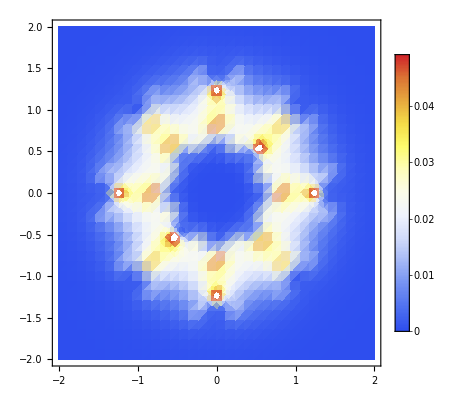
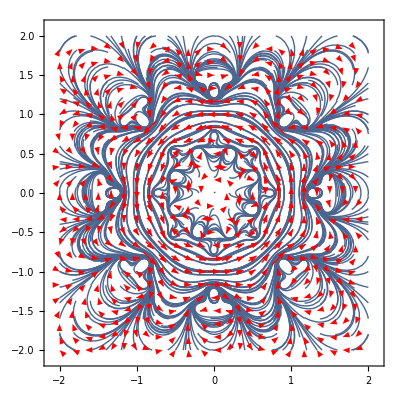

```mathematica
Overlay[{DensityPlot[Norm[ElmoBumpyCartWedge[X,Y,1.2566*^-6,10000,8,1,0.25,0.2,2500]],{X,-2,2},{Y,-2,2},ColorFunction->"TemperatureMap",PlotPoints->35,PlotLegends->Automatic],StreamPlot[ElmoBumpyCartWedge[X,Y,1.2566*^-6,10000,8,1,0.25,0.2,2500],{X,-2,2},{Y,-2,2},StreamPoints->{Tuples[Range[-2,2,0.2],2],Automatic,2},StreamStyle->"Line",VectorPoints->Fine,VectorPoints->10,VectorStyle->Red]}]
```